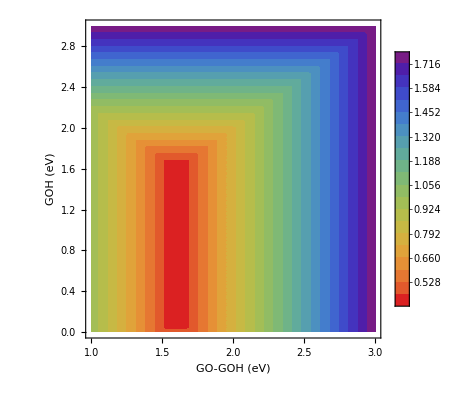

```mathematica
U=0;
Gooh=1*Goh+3.2;
G1=Goh-e U;
G2=Go-Goh-e U;
G3=Gooh-Go-e U;
G4=4.92-Gooh-e U;
n=Max[G1,G2,G3,G4]-1.23;
Volcano=ContourPlot[n,{diff,1,3},{Goh,0,3},PlotLegends->Automatic,Exclusions->None,ContourStyle->None, Contours->20,ColorFunction-> ColorData[{"Rainbow","Reverse"}],ContourStyle->None,PlotTheme-> "Web",FrameLabel->{Style["GO-GOH (eV)",Large,Black],Style["GOH (eV)",Large,Black]},LabelStyle->Directive[Medium,Black],Exclusions->None]
```